```mathematica
Clear["Global`*"]
```

```mathematica
(*experiment data*)
Δ=Transpose[Import["/Users/mac/Desktop/spin liquid/data/Fig1E.txt","Table"]][[1]];
(*the number of monomer*)
Nmon=Transpose[Import["/Users/mac/Desktop/spin liquid/data/Fig1E.txt","Table"]][[7]];
(*the number of dimer*)
Ndim=Transpose[Import["/Users/mac/Desktop/spin liquid/data/Fig1E.txt","Table"]][[8]];
```

```mathematica
(*4*4*)(*configuration number*)
f=Import["/Users/mac/Desktop/spin liquid/data/log_basis_4_4.txt","Table"][[1]];
fz=Import["/Users/mac/Desktop/spin liquid/data/log_basis_4_4.txt","Table"][[2]];
fzopen=Import["/Users/mac/Desktop/spin liquid/data/log_basis_4_4.txt","Table"][[3]];
fx=Import["/Users/mac/Desktop/spin liquid/data/log_basis_4_4.txt","Table"][[4]];
f0=Import["/Users/mac/Desktop/spin liquid/data/log_basis_4_4.txt","Table"][[5]];
fp=Import["/Users/mac/Desktop/spin liquid/data/log_basis_4_4.txt","Table"][[6]];
fm=Import["/Users/mac/Desktop/spin liquid/data/log_basis_4_4.txt","Table"][[7]];
```

```mathematica
Nb=4*4*6;
(*normalization facor*)
Ntot[v_]:=Sum[f[[i+1]]*v^(2*i),{i,0,(Length[f]-1)}];
Nmo[v_]:=Sum[2*(1/2*Nb-2i)*f[[i+1]]*v^(2*i)/(Nb*Ntot[v]),{i,0,(Length[f]-1)}];
Z[v_]:=Sum[(2*fz[[i+1]]-f[[i+1]])*v^(2*i)/Ntot[v],{i,0,(Length[f]-1)}];
X[v_]:=Sum[fx[[i+1]]*v^(2*i)/Ntot[v],{i,0,(Length[f]-1)}];
Zopen[v_]:=Sum[(2*fzopen[[i+1]]-f[[i+1]])*v^(2*i)/Ntot[v],{i,0,(Length[f]-1)}];
Xopen[v_]:=Sum[(f0[[i+1]]*v^(2*i)-fp[[i+1]]*v^(2*i+1)-fm[[i+1]]*v^(2*i-1))/Ntot[v],{i,0,(Length[f]-1)}];
(*energy*)
E1[v_]:=-Sum[i*f[[i+1]] v^(2*i-1),{i,1,(Length[f]-1)}]/Ntot[v];
E2[v_]:=Sum[(Nb-2*i)/2*f[[i+1]] v^(2*i),{i,0,(Length[f]-1)}]/Ntot[v];
Etot[v_,h_]:=E1[v]+h*E2[v];
```

```mathematica
resv={};
resZ={};
resX={};
resZopen={};
resXopen={};
resE={};
For[i=1,i<Length[Δ],i=i+1,a=v/.Flatten[NSolve[{Nmo[v]==Nmon[[i]],v>0}]];
AppendTo[resv,{Δ[[i]],a}];
AppendTo[resZ,{Δ[[i]],Z[a]}];
AppendTo[resX,{Δ[[i]],X[a]}];
AppendTo[resZopen,{Δ[[i]],Zopen[a]}];
AppendTo[resXopen,{Δ[[i]],Xopen[a]}];
AppendTo[resE,{Δ[[i]],Etot[a,Δ[[i]]]/Nb}];]
```

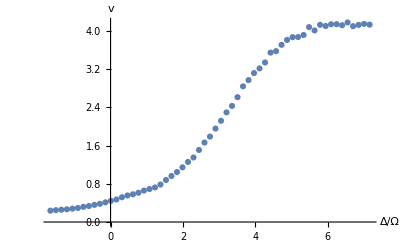

```mathematica
ListPlot[resv,AxesLabel->{HoldForm[Δ/Ω],HoldForm[v]},AxesStyle->Directive[Black,15,FontFamily->"Times"]]
```

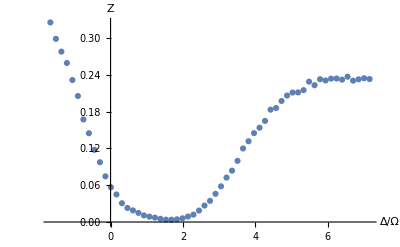

```mathematica
ListPlot[resZ,AxesLabel->{HoldForm[Δ/Ω],HoldForm[Z]},AxesStyle->Directive[Black,15,FontFamily->"Times"]]
```

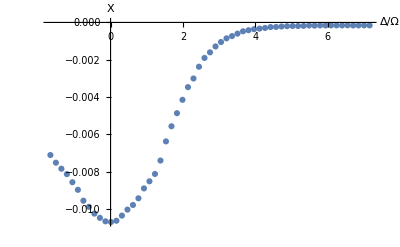

```mathematica
ListPlot[resXopen,AxesLabel->{HoldForm[Δ/Ω],HoldForm[X]},AxesStyle->Directive[Black,15,FontFamily->"Times"]]
```

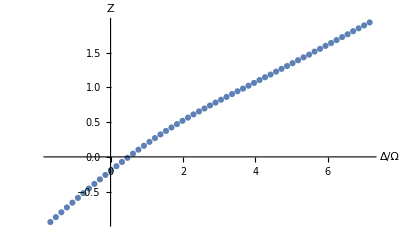

```mathematica
ListPlot[resE,AxesLabel->{HoldForm[Δ/Ω],HoldForm[Z]},AxesStyle->Directive[Black,15,FontFamily->"Times"]]
```